```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
GreedyAlgorithmFromCost[Cost_]:=((* 入力として枝のコストを与えられたときのGreedyアルゴリズムによる解法 *)
SortList=Ordering[Cost//N];(* 昇順 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
If[Length[VertexList[FindCycle[UndirectedGraph[AppendEdgeProcess]][[1]]]]==Length[Pin],EdgeSolution=AppendEdgeProcess]
]
]
];
EdgeSolution=FindCycle[UndirectedGraph[EdgeSolution]][[1]];
VertexSolution={1};
For[j=1,Length[VertexSolution]≠ Length[EdgeSolution],j++,
VertexSolution=Append[VertexSolution,EdgeSolution[[FirstPosition[EdgeSolution,VertexSolution[[j]]<->_][[1]],2]]]
];
VertexSolution=Append[VertexSolution,1]
)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
```

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

$Aborted

### TSPの解

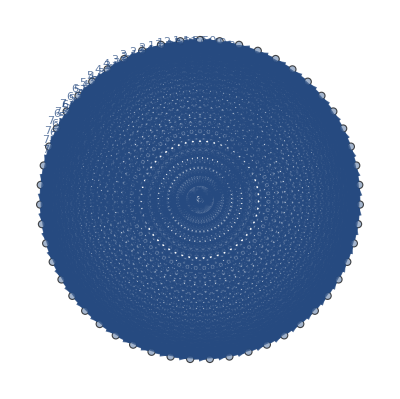
Transpose[LoopMatrix[-Graphics-]].Inverse[LoopMatrix[-Graphics-].{1}.Transpose[LoopMatrix[-Graphics-]]].{}
 |  |  |  |

```mathematica
Curr
```

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{1}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{1265,769,700,413,679,530,31,301,638,1140,1002,412,476,583,1138,482,639,1048,1116,21,227,529,794,347,631,818,401,1177,160,161,453,1195,116,190,839,379,999,26,534,743,238,980,393,64,707,770,996,282,397,77,261,823,201,352,369,434,658,667,710,894,994,1099,562,870,1269,124,500,1261,443,460,1104,131,520,650,788,846,955,1063,490,1064,248,576,1232,1248,59,70,768,582,200,257,304,721,1043,1196,226,326,80,285,611,7,627,850,68,235,321,373,495,663,1053,1273,10,132,343,437,1210,118,1180,1,47,198,916,155,795,180,374,349,849,889,1091,1221,546,972,184,384,280,678,1192,50,98,471,1178,45,258,1110,1137,286,348,501,898,240,681,199,302,456,493,521,705,539,540,86,204,252,494,69,162,206,747,187,661,845,156,781,236,442,659,1052,51,1027,281,581,819,1028,872,438,515,127,344,419,1101,1197,1272,466,185,510,952,221,1126,27,392,636,742,57,205,449,1175,605,241,1211,259,787,873,5,454,498,709,780,995,1115,643,30,1179,266,527,1207,125,1182,772,866,194,682,714,921,239,353,473,532,737,1262,168,189,708,649,1250,157,1233,233,242,246,704,609,1120,1127,1184,219,847,535,606,827,1031,1171,1082,1108,15,733,844,37,25,158,651,76,585,946,561,75,441,83,395,1100,2,491,402,641,1006,1263,94,838,305,723,986,82,234,420,465,675,1007,1025,1223,1103,1258,604,951,1193,148,715,216,864,1102,478,1203,869,1047,11,19,222,309,409,853,824,1023,53,97,99,149,375,632,720,765,809,871,104,568,223,940,1226,474,28,481,497,22,292,712,1003,1029,701,1019,1274,245,260,448,415,563,1244,372,492,680,897,538,979,4,56,740,856,1208,1252,900,967,1042,1235,775,791,1174,464,128,6,400,416,790,499,112,1266,367,633,696,976,1066,414,601,656,950,207,613,256,46,79,277,378,640,738,1267,528,744,461,332,425,78,396,531,719,421,892,1249,1264,117,170,525,664,854,877,8,49,228,575,1000,821,84,868,1185,624,878,956,728,96,251,508,645,1090,60,947,188,899,183,688,811,1113,1190,1254,945,1109,210,924,107,345,599,926,690,122,793,218,195,383,533,612,695,1059,300,459,753,1069,1191,524,797,385,841,1070,472,635,364,942,985,1256,450,502,773,1275,462,920,306,341,590,48,329,408,1087,1051,181,893,1213,154,390,516,1154,272,175,997,13,20,303,380,496,565,668,310,410,825,211,545,558,828,123,247,265,146,919,34,271,505,513,1105,657,1039,17,231,335,666,1046,703,433,1172,977,54,58,192,734,975,436,451,998,595,1194,324,1183,455,407,475,144,676,167,488,1060,786,874,1121,23,644,1202,577,74,1044,237,506,572,95,1088,191,970,736,867,1134,610,936,991,337,1024,262,479,134,1085,1224,1255,1022,296,333,458,517,584,1123,626,665,1017,835,628,865,36,350,359,567,677,1080,1118,203,1058,507,1230,176,467,368,905,33,852,16,646,1065,470,105,356,789,1125,1234,3,35,483,1225,489,166,477,693,941,808,1239,1260,512,1173,153,745,805,817,1268,250,662,398,785,660,1139,741,1133,85,208,779,1259,275,446,142,325,931,1097,711,840,939,1009,807,339,713,774,1117,130,536,1077,602,810,1237,943,147,621,816,504,634,29,230,1021,152,209,357,522,1142,1169,1216,702,992,283,1032,24,761,197,278,600,739,289,1061,580,674,904,596,1041,1181,544,346,71,214,548,1089,848,1122,9,243,290,65,673,1253,42,431,1214,842,249,982,718,1188,1247,687,411,55,253,1072,381,480,978,103,914,469,391,159,983,102,202,371,959,573,87,697,63,1270,468,686,66,822,330,1132,1271,647,14,960,1098,1135,101,422,569,826,925,971,1124,212,1204,145,509,1049,284,619,722,855,884,119,598,1040,1112,503,523,615,1030,589,655,820,1242,1086,342,953,989,276,511,52,263,729,426,150,217,566,685,1084,486,1092,126,424,514,962,1096,151,193,254,399,43,62,861,1153,1243,1152,165,173,370,1205,777,901,937,1014,108,1209,836,1200,910,1150,1005,1157,883,405,607,213,423,623,766,1081,755,92,394,564,990,993,81,220,553,984,338,746,837,752,1020,1018,1187,652,834,1155,1228,316,224,244,1095,586,684,692,843,291,1026,485,358,574,215,196,93,298,457,463,1094,1251,887,1167,182,642,911,1056,186,1227,377,782,72,279,727,445,1111,295,526,559,806,981,255,294,760,616,726,177,355,12,143,603,833,44,264,1136,948,1220,1050,268,229,974,1083,1038,944,169,1215,1001,452,724,32,875,106,389,38,798,917,570,930,1165,895,386,1068,1037,1062,73,439,487,815,307,315,554,725,1168,776,862,382,796,518,671,172,987,1170,915,730,269,274,751,40,351,1238,890,608,418,267,896,41,164,404,313,689,654,973,1236,334,225,388,857,653,120,618,331,617,110,735,18,717,767,287,683,913,1130,417,927,174,336,961,1008,314,587,881,91,133,319,706,922,432,591,114,327,691,328,614,1045,139,171,365,694,863,758,1257,429,716,851,888,1071,1222,270,376,578,387,90,648,932,113,1143,1151,547,1218,670,444,588,812,882,232,958,988,163,519,543,949,1055,1199,778,792,783,1186,1189,440,135,537,299,362,1119,100,273,322,592,1176,435,579,61,297,902,1229,427,923,89,111,293,803,1141,67,484,880,859,804,954,622,860,876,771,1093,121,928,762,831,886,929,340,918,672,891,802,571,1206,366,750,430,620,1217,363,428,625,551,1035,1166,968,320,698,312,1129,1015,140,629,965,784,288,731,354,1158,403,597,593,933,129,552,1010,1078,308,360,1198,560,813,1240,908,814,1036,1106,141,879,903,178,39,1245,406,907,1156,1231,555,549,906,754,938,749,757,1054,1147,1004,637,1016,1034,323,909,1148,830,594,1246,550,1149,1212,1162,318,966,1073,699,732,1075,669,1079,969,542,630,1067,1219,1012,801,885,311,934,179,759,957,109,832,1013,1076,1107,88,541,361,756,963,1128,138,800,748,447,858,912,137,1163,1164,317,1241,935,1131,115,1057,964,1146,829,1033,1114,556,1145,763,1074,1011,1161,557,1201,799,1160,136,764,1144,1159}

```mathematica
NewCost=Abs[PD/Curr ]
```

$Aborted[]

{13.8922,{1,3,4,6,5,2,1}}

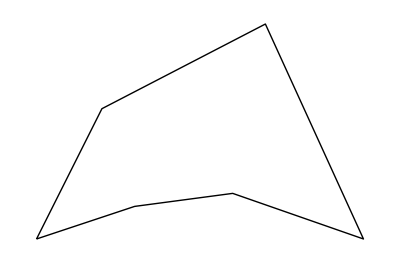

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
GreedyAlgorithmFromCost[PD]
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,2,5,6,4,3,1}

-Graphics-

{1,4,3,6,5,2,1}

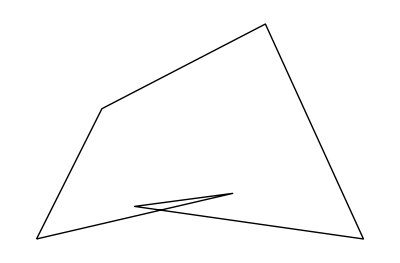

```mathematica
GreedyAlgorithmFromCost[Abs[1/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

```mathematica
GreedyAlgorithmFromCost[Curr](* 正負のあるCurrでなぜ最適解が求められたのかわからない *)
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,3,4,6,5,2,1}

-Graphics-

```mathematica
GreedyAlgorithmFromCost[Abs[PD/Curr]]
Graphics[Line[Pin[[VertexSolution]]]]
```

{1,2,5,6,4,3,1}

-Graphics-

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]]
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
ArcLength[Line[Pin[[VertexSolution]]]]//N
```

481.519